```mathematica
Clear[g,gg,i]
g25=Monitor[Table[Table[Table[#[[1,3]]&/@TuringMachine[i,{{1,-2,0},{IntegerDigits[j,2,20],0}},1000],{i,1,4095}],{j,21,25}]],{i,j}];
```

```mathematica
Clear[g,gg,i]
g30=Monitor[Table[Table[Table[#[[1,3]]&/@TuringMachine[i,{{1,-2,0},{IntegerDigits[j,2,20],0}},1000],{i,1,4095}],{j,26,30}]],{i,j}];
```

```mathematica
Clear[g,gg,i]
g35=Monitor[Table[Table[Table[#[[1,3]]&/@TuringMachine[i,{{1,-2,0},{IntegerDigits[j,2,20],0}},1000],{i,1,4095}],{j,31,35}]],{i,j}];
```

```mathematica
Clear[g,gg,i]
g40=Monitor[Table[Table[Table[#[[1,3]]&/@TuringMachine[i,{{1,-2,0},{IntegerDigits[j,2,20],0}},1000],{i,1,4095}],{j,36,40}]],{i,j}];
```

```mathematica
Clear[g,gg,i]
g45=Monitor[Table[Table[Table[#[[1,3]]&/@TuringMachine[i,{{1,-2,0},{IntegerDigits[j,2,20],0}},1000],{i,1,4095}],{j,41,45}]],{i,j}];
Clear[g,gg,i]
g50=Monitor[Table[Table[Table[#[[1,3]]&/@TuringMachine[i,{{1,-2,0},{IntegerDigits[j,2,20],0}},1000],{i,1,4095}],{j,46,50}]],{i,j}];
```

$Aborted

$Aborted

{«1»}

{-16994797/225450,-6801401/90180,-16999103/225450,-11337419/150300,-944542/12525,-8149/108,-5667407/75150,-1360957/18036,-8501401/112725,-34021901/450900,-3400829/45090,-34017463/450900,-680029/9018,-6802223/90180,-1699781/22545,-11339267/150300,-8498999/112725,-1259787/16700,-50891/675,-11338399/150300,-8500313/112725,-3779357/50100,-5666299/75150,-6801901/90180,-8499013/112725,-34010353/450900,-8498161/112725,-6801521/90180,-8496887/112725,-3778079/50100,-8497543/112725,-34005739/450900,-5665417/75150,-34003783/450900,-2831863/37575,-3777869/50100,-2831593/37575,-33994831/450900,-16987177/225450,-33984007/450900,-8493118/112725,-33977531/450900,-3396007/45090,-6794953/90180,-2829173/37575,-16986173/225450,-5658607/75150,-16986089/225450,-1697762/22545,-8489393/112725,-16974391/225450,-2829673/37575,-2828186/37575,-5657911/75150,-2826931/37575,-943018/12525,-16965517/225450,-2829137/37575,-942454/12525,-5656529/75150,-16966721/225450,-339496/4509,-3393881/45090,-3395083/45090,-5655341/75150,-16975817/225450,-5655589/75150,-1697566/22545,-8482469/112725,-16971361/225450,-8484652/112725,-377257/5010,-942893/12525,-1697486/22545,-2827846/37575,-16978859/225450,-8486398/112725,-2830229/37575,-8486789/112725,-16981943/225450,-8488789/112725,-8492071/112725,-943141/12525,-8491033/112725,-8487172/112725,-943558/12525,-8487454/112725,-16983127/225450,-16973167/225450,-679295/9018,-943166/12525,-943643/12525,-8489902/112725,-377461/5010,-16981631/225450,-8496293/112725,-50857/675,-8497394/112725,-8493454/112725,-16997717/225450}

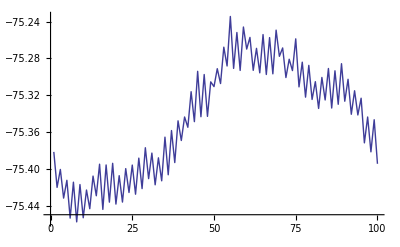

```mathematica
G[x_]:={ListLinePlot[Re[x]],ListLinePlot[Im[x]]}
h=Partition[Flatten[{g5,g10}],100]
Mean[h]
ListLinePlot[%]
```

```mathematica
G[x_]:={ListLinePlot[Re[x]],ListLinePlot[Im[x]]}
h2=Partition[Flatten[{h,g15,g20}],100]
Mean[h]
ListLinePlot[%]
```

{{0,-1,-2,-3,-4,-5,-6,-7,-8,-9,-10,-11,-12,-13,-14,-15,-16,-17,-18,-19,-20,-21,-22,-23,-24,-25,-26,-27,-28,-29,-30,-31,-32,-33,-34,-35,-36,-37,-38,-39,«21»,-61,-62,-63,-64,-65,-66,-67,-68,-69,-70,-71,-72,-73,-74,-75,-76,-77,-78,-79,-80,-81,-82,-83,-84,-85,-86,-87,-88,-89,-90,-91,-92,-93,-94,-95,-96,-97,-98,-99},«860808»}

{-16994797/225450,-6801401/90180,-16999103/225450,-11337419/150300,-944542/12525,-8149/108,-5667407/75150,-1360957/18036,-8501401/112725,-34021901/450900,-3400829/45090,-34017463/450900,-680029/9018,-6802223/90180,-1699781/22545,-11339267/150300,-8498999/112725,-1259787/16700,-50891/675,-11338399/150300,-8500313/112725,-3779357/50100,-5666299/75150,-6801901/90180,-8499013/112725,-34010353/450900,-8498161/112725,-6801521/90180,-8496887/112725,-3778079/50100,-8497543/112725,-34005739/450900,-5665417/75150,-34003783/450900,-2831863/37575,-3777869/50100,-2831593/37575,-33994831/450900,-16987177/225450,-33984007/450900,-8493118/112725,-33977531/450900,-3396007/45090,-6794953/90180,-2829173/37575,-16986173/225450,-5658607/75150,-16986089/225450,-1697762/22545,-8489393/112725,-16974391/225450,-2829673/37575,-2828186/37575,-5657911/75150,-2826931/37575,-943018/12525,-16965517/225450,-2829137/37575,-942454/12525,-5656529/75150,-16966721/225450,-339496/4509,-3393881/45090,-3395083/45090,-5655341/75150,-16975817/225450,-5655589/75150,-1697566/22545,-8482469/112725,-16971361/225450,-8484652/112725,-377257/5010,-942893/12525,-1697486/22545,-2827846/37575,-16978859/225450,-8486398/112725,-2830229/37575,-8486789/112725,-16981943/225450,-8488789/112725,-8492071/112725,-943141/12525,-8491033/112725,-8487172/112725,-943558/12525,-8487454/112725,-16983127/225450,-16973167/225450,-679295/9018,-943166/12525,-943643/12525,-8489902/112725,-377461/5010,-16981631/225450,-8496293/112725,-50857/675,-8497394/112725,-8493454/112725,-16997717/225450}

-Graphics-

```mathematica
h3=Partition[Flatten[{g25,g30}],100]
```

{-36578261/409909,-36584266/409909,-36587569/409909,-36583290/409909,-36587989/409909,-36592798/409909,-36598109/409909,-36602362/409909,-36601931/409909,-36608958/409909,-36612505/409909,-36610280/409909,-36611839/409909,-36612064/409909,-36617419/409909,-36619170/409909,-36610761/409909,-36617166/409909,-36611953/409909,-36613172/409909,-36615601/409909,-36613216/409909,-36618321/409909,-36615886/409909,-36619135/409909,-36620236/409909,-36618067/409909,-36616974/409909,-36612971/409909,-36612048/409909,-36612077/409909,-36607678/409909,-36611147/409909,-36609122/409909,-36608939/409909,-36611954/409909,-36608729/409909,-36611930/409909,-36611943/409909,-36607594/409909,-36611799/409909,-36611562/409909,-36612379/409909,-36608700/409909,-36597631/409909,-36603682/409909,-36597467/409909,-36596594/409909,-36593371/409909,-36585578/409909,-36588596/409909,-36580676/409909,-36579556/409909,-36577190/409909,-36569438/409909,-36574668/409909,-36566016/409909,-36564774/409909,-36557296/409909,-36547020/409909,-36552888/409909,-36553920/409909,-36553096/409909,-36548798/409909,-36541814/409909,-36552412/409909,-36555052/409909,-36555752/409909,-36550084/409909,-36548162/409909,-36555736/409909,-36555820/409909,-36554614/409909,-36552224/409909,-36544912/409909,-36554520/409909,-36552340/409909,-36557694/409909,-36553668/409909,-36550258/409909,-36557382/409909,-36559638/409909,-36559716/409909,-36557760/409909,-36554432/409909,-36564820/409909,-36562116/409909,-36559858/409909,-36549584/409909,-36553194/409909,-36559688/409909,-36559412/409909,-36559516/409909,-36558070/409909,-36562132/409909,-36565442/409909,-36565436/409909,-36570698/409909,-36566382/409909,-36571698/409909}

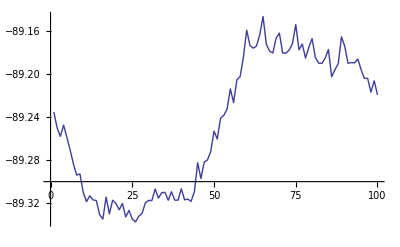

```mathematica
Mean[h3]
ListLinePlot[%]
```

```mathematica
20*4095*1000*{-16994797/225450,-6801401/90180,-16999103/225450,-11337419/150300,-944542/12525,-8149/108,-5667407/75150,-1360957/18036,-8501401/112725,-34021901/450900,-3400829/45090,-34017463/450900,-680029/9018,-6802223/90180,-1699781/22545,-11339267/150300,-8498999/112725,-1259787/16700,-50891/675,-11338399/150300,-8500313/112725,-3779357/50100,-5666299/75150,-6801901/90180,-8499013/112725,-34010353/450900,-8498161/112725,-6801521/90180,-8496887/112725,-3778079/50100,-8497543/112725,-34005739/450900,-5665417/75150,-34003783/450900,-2831863/37575,-3777869/50100,-2831593/37575,-33994831/450900,-16987177/225450,-33984007/450900,-8493118/112725,-33977531/450900,-3396007/45090,-6794953/90180,-2829173/37575,-16986173/225450,-5658607/75150,-16986089/225450,-1697762/22545,-8489393/112725,-16974391/225450,-2829673/37575,-2828186/37575,-5657911/75150,-2826931/37575,-943018/12525,-16965517/225450,-2829137/37575,-942454/12525,-5656529/75150,-16966721/225450,-339496/4509,-3393881/45090,-3395083/45090,-5655341/75150,-16975817/225450,-5655589/75150,-1697566/22545,-8482469/112725,-16971361/225450,-8484652/112725,-377257/5010,-942893/12525,-1697486/22545,-2827846/37575,-16978859/225450,-8486398/112725,-2830229/37575,-8486789/112725,-16981943/225450,-8488789/112725,-8492071/112725,-943141/12525,-8491033/112725,-8487172/112725,-943558/12525,-8487454/112725,-16983127/225450,-16973167/225450,-679295/9018,-943166/12525,-943643/12525,-8489902/112725,-377461/5010,-16981631/225450,-8496293/112725,-50857/675,-8497394/112725,-8493454/112725,-16997717/225450}
```

{-3093053054000/501,-3094637455000/501,-3093836746000/501,-1031705129000/167,-1031439864000/167,-18538975000/3,-1031468074000/167,-3096177175000/501,-3094509964000/501,-3095992991000/501,-3094754390000/501,-3095589133000/501,-3094131950000/501,-3095011465000/501,-3093601420000/501,-1031873297000/167,-3093635636000/501,-1031765553000/167,-18524324000/3,-1031794309000/167,-3094113932000/501,-1031764461000/167,-1031266418000/167,-3094864955000/501,-3093640732000/501,-3094942123000/501,-3093330604000/501,-3094692055000/501,-3092866868000/501,-1031415567000/167,-3093105652000/501,-3094522249000/501,-1031105894000/167,-3094344253000/501,-1030798132000/167,-1031358237000/167,-1030699852000/167,-3093529621000/501,-3091666214000/501,-3092544637000/501,-3091494952000/501,-3091955321000/501,-3090366370000/501,-3091703615000/501,-1029818972000/167,-3091483486000/501,-1029866474000/167,-3091468198000/501,-3089926840000/501,-3090139052000/501,-3089339162000/501,-1030000972000/167,-1029459704000/167,-1029739802000/167,-1029002884000/167,-1029775656000/167,-3087724094000/501,-1029805868000/167,-1029159768000/167,-1029488278000/167,-3087943222000/501,-3089413600000/501,-3088431710000/501,-3089525530000/501,-1029272062000/167,-3089598694000/501,-1029317198000/167,-3089570120000/501,-3087618716000/501,-3088787702000/501,-3088413328000/501,-1029911610000/167,-1029639156000/167,-3089424520000/501,-1029335944000/167,-3090152338000/501,-3089048872000/501,-1030203356000/167,-3089191196000/501,-3090713626000/501,-3089919196000/501,-3091113844000/501,-1029909972000/167,-3090736012000/501,-3089330608000/501,-1030365336000/167,-3089433256000/501,-3090929114000/501,-3089116394000/501,-3090792250000/501,-1029937272000/167,-1030458156000/167,-3090324328000/501,-1030468530000/167,-3090656842000/501,-3092650652000/501,-18511948000/3,-3093051416000/501,-3091617256000/501,-3093584494000/501}

```mathematica
pn[s_]:=FindInstance[Table[Total[Table[Subscript[a, i]*j^(i-1),{i,1,Length[s]}]]==s[[j]],{j,1,Length[s]}],Table[Subscript[a, i],{i,1,Length[s]}],Reals]
```

```mathematica
i[in_]:=Table[Last[Flatten[in][[i]]],{i,1,Length[Flatten[in]]}]
```

```mathematica
po[s_]:=Total[Table[(s[[i]])*j^(i-1),{i,1,Length[s]}]]
```

```mathematica
Mean[Partition[Flatten[Monitor[Table[Table[Table[#[[1,3]]&/@TuringMachine[i,{{1,-2,0},{IntegerDigits[j,2,20],0}},1000],{i,1,4095}],{j,1,1}]],{i,j}]],1000]]
```

{-438201/4099,-441209/4099,-439611/4099,-441791/4099,-438261/4099,-442243/4099,-438961/4099,-442945/4099,-441431/4099,-444937/4099,-444337/4099,-447873/4099,-445137/4099,-448145/4099,-445705/4099,-448413/4099,-447303/4099,-450795/4099,-450687/4099,-453521/4099,-451095/4099,-454091/4099,-450835/4099,-453491/4099,-451069/4099,-452557/4099,-450451/4099,-451991/4099,-448261/4099,-449289/4099,-445671/4099,-446717/4099,-444745/4099,-446735/4099,-446139/4099,-448173/4099,-445413/4099,-446421/4099,-443819/4099,-444523/4099,-443117/4099,-445093/4099,-443975/4099,-446013/4099,-443605/4099,-445565/4099,-443623/4099,-445597/4099,-442853/4099,-442841/4099,-440561/4099,-440589/4099,-436853/4099,-435865/4099,-432251/4099,-431287/4099,-428555/4099,-428547/4099,-425949/4099,-425979/4099,-422563/4099,-421555/4099,-418277/4099,-416971/4099,-416247/4099,-418227/4099,-417429/4099,-419433/4099,-417697/4099,-419663/4099,-418381/4099,-420345/4099,-418605/4099,-418587/4099,-417329/4099,-417329/4099,-414605/4099,-414595/4099,-411967/4099,-411979/4099,-410247/4099,-410213/4099,-408095/4099,-408123/4099,-405389/4099,-404381/4099,-401773/4099,-400461/4099,-399761/4099,-400787/4099,-400515/4099,-401545/4099,-400855/4099,-401863/4099,-401613/4099,-401642/4099,-400919/4099,-400930/4099,-400345/4099,-400370/4099,-399665/4099,-399660/4099,-399055/4099,-399072/4099,-398365/4099,-398360/4099,-397757/4099,-397786/4099,-397057/4099,-397052/4099,-396451/4099,-396462/4099,-397745/4099,-399752/4099,-399833/4099,-401840/4099,-401169/4099,-403138/4099,-402575/4099,-404608/4099,-405857/4099,-407832/4099,-407907/4099,-409904/4099,-409217/4099,-411176/4099,-410575/4099,-412570/4099,-411833/4099,-411804/4099,-409867/4099,-409850/4099,-407139/4099,-407094/4099,-404513/4099,-404496/4099,-404763/4099,-405764/4099,-404503/4099,-405512/4099,-402859/4099,-404802/4099,-402255/4099,-402936/4099,-403195/4099,-404160/4099,-402915/4099,-403916/4099,-401263/4099,-403240/4099,-400665/4099,-402634/4099,-401883/4099,-401830/4099,-399567/4099,-399356/4099,-395665/4099,-395608/4099,-392051/4099,-391696/4099,-390949/4099,-390924/4099,-388643/4099,-388622/4099,-384971/4099,-385898/4099,-382329/4099,-383310/4099,-382569/4099,-382538/4099,-380289/4099,-380266/4099,-376601/4099,-377544/4099,-373983/4099,-374936/4099,-372199/4099,-370170/4099,-367215/4099,-366198/4099,-362471/4099,-361418/4099,-357831/4099,-356800/4099,-354075/4099,-352056/4099,-349091/4099,-346756/4099,-343075/4099,-341052/4099,-337459/4099,-335156/4099,-334363/4099,-334298/4099,-333321/4099,-334238/4099,-332499/4099,-333426/4099,-331779/4099,-332720/4099,-330945/4099,-329866/4099,-328205/4099,-327170/4099,-325389/4099,-324304/4099,-322629/4099,-321570/4099,-319783/4099,-318734/4099,-317051/4099,-315998/4099,-314227/4099,-313140/4099,-311481/4099,-310438/4099,-309325/4099,-308946/4099,-307977/4099,-307628/4099,-306535/4099,-306166/4099,-305179/4099,-304826/4099,-303755/4099,-303372/4099,-302399/4099,-302060/4099,-300969/4099,-300592/4099,-299631/4099,-299280/4099,-298209/4099,-297864/4099,-296887/4099,-296544/4099,-295475/4099,-295098/4099,-294139/4099,-293824/4099,-294691/4099,-296276/4099,-297275/4099,-298880/4099,-297857/4099,-299460/4099,-298533/4099,-300148/4099,-301079/4099,-302724/4099,-303751/4099,-305422/4099,-306347/4099,-307984/4099,-309049/4099,-310712/4099,-308375/4099,-307758/4099,-305529/4099,-304560/4099,-301591/4099,-301948/4099,-299081/4099,-299450/4099,-299107/4099,-300796/4099,-300589/4099,-302060/4099,-301083/4099,-303660/4099,-302787/4099,-305164/4099,-304891/4099,-306552/4099,-304975/4099,-306182/4099,-304203/4099,-306846/4099,-304065/4099,-306728/4099,-305689/4099,-307688/4099,-305773/4099,-306952/4099,-303391/4099,-306054/4099,-303487/4099,-304896/4099,-302849/4099,-303848/4099,-301759/4099,-302114/4099,-299435/4099,-302424/4099,-299867/4099,-302496/4099,-301651/4099,-303618/4099,-301193/4099,-303046/4099,-300371/4099,-304300/4099,-302067/4099,-305640/4099,-303891/4099,-305874/4099,-303443/4099,-304502/4099,-300885/4099,-303892/4099,-301293/4099,-303962/4099,-300905/4099,-301856/4099,-298777/4099,-299404/4099,-295703/4099,-299692/4099,-296105/4099,-299740/4099,-298051/4099,-301012/4099,-299595/4099,-301992/4099,-299303/4099,-303272/4099,-301027/4099,-304662/4099,-301923/4099,-303930/4099,-301801/4099,-302860/4099,-299147/4099,-302160/4099,-298533/4099,-299946/4099,-297225/4099,-299202/4099,-296607/4099,-298060/4099,-294335/4099,-298350/4099,-294745/4099,-298712/4099,-297027/4099,-300002/4099,-298863/4099,-300756/4099,-297017/4099,-301008/4099,-297409/4099,-300090/4099,-298343/4099,-301338/4099,-299895/4099,-302540/4099,-298825/4099,-301840/4099,-298207/4099,-300902/4099,-299155/4099,-301146/4099,-299869/4099,-301892/4099,-298141/4099,-302138/4099,-298513/4099,-302464/4099,-301757/4099,-305740/4099,-304785/4099,-308166/4099,-304431/4099,-308422/4099,-304825/4099,-308472/4099,-307727/4099,-311722/4099,-311265/4099,-314932/4099,-311217/4099,-315204/4099,-311589/4099,-315264/4099,-313553/4099,-316208/4099,-314935/4099,-316794/4099,-313049/4099,-315738/4099,-312115/4099,-314638/4099,-313931/4099,-315616/4099,-315161/4099,-316504/4099,-312775/4099,-316090/4099,-312491/4099,-314156/4099,-313419/4099,-316098/4099,-315163/4099,-317682/4099,-313975/4099,-317592/4099,-313967/4099,-317440/4099,-315707/4099,-317048/4099,-315775/4099,-316786/4099,-313071/4099,-314600/4099,-310993/4099,-311934/4099,-310211/4099,-311538/4099,-309605/4099,-309332/4099,-305601/4099,-308616/4099,-305019/4099,-307518/4099,-305797/4099,-307130/4099,-304973/4099,-306980/4099,-303261/4099,-306886/4099,-303263/4099,-306728/4099,-303973/4099,-304308/4099,-302035/4099,-302506/4099,-298777/4099,-300216/4099,-296597/4099,-298888/4099,-296157/4099,-296484/4099,-293521/4099,-293210/4099,-289483/4099,-293432/4099,-289817/4099,-293394/4099,-291329/4099,-292998/4099,-291231/4099,-293192/4099,-290139/4099,-293766/4099,-290841/4099,-294472/4099,-291405/4099,-293078/4099,-290137/4099,-291090/4099,-288695/4099,-290356/4099,-287741/4099,-289100/4099,-286067/4099,-287698/4099,-284775/4099,-285912/4099,-282857/4099,-286230/4099,-283307/4099,-286620/4099,-284247/4099,-285938/4099,-283667/4099,-285334/4099,-283629/4099,-287274/4099,-285141/4099,-287512/4099,-285651/4099,-288650/4099,-286967/4099,-289496/4099,-287117/4099,-290104/4099,-287811/4099,-290466/4099,-288081/4099,-289748/4099,-287473/4099,-289286/4099,-286219/4099,-289906/4099,-286975/4099,-290592/4099,-288833/4099,-292814/4099,-291145/4099,-294412/4099,-292699/4099,-296688/4099,-294565/4099,-298226/4099,-296231/4099,-300226/4099,-298761/4099,-301190/4099,-299825/4099,-303818/4099,-301529/4099,-305200/4099,-302981/4099,-304948/4099,-303175/4099,-304414/4099,-300695/4099,-302736/4099,-299145/4099,-300918/4099,-298775/4099,-299600/4099,-298309/4099,-298776/4099,-297063/4099,-299058/4099,-297329/4099,-297836/4099,-296081/4099,-298118/4099,-296651/4099,-298592/4099,-297227/4099,-300202/4099,-297921/4099,-300904/4099,-298185/4099,-298170/4099,-296403/4099,-296106/4099,-292377/4099,-292210/4099,-288621/4099,-288298/4099,-285585/4099,-285598/4099,-283463/4099,-282220/4099,-279847/4099,-279840/4099,-277247/4099,-276936/4099,-274215/4099,-274252/4099,-271895/4099,-272748/4099,-270047/4099,-271038/4099,-268755/4099,-269750/4099,-266533/4099,-264530/4099,-262271/4099,-261282/4099,-257553/4099,-256542/4099,-252943/4099,-251932/4099,-248709/4099,-246716/4099,-243583/4099,-241292/4099,-237565/4099,-235552/4099,-231955/4099,-229640/4099,-228387/4099,-228400/4099,-227987/4099,-228966/4099,-228243/4099,-229222/4099,-228923/4099,-229942/4099,-228217/4099,-227180/4099,-225563/4099,-224582/4099,-222845/4099,-221844/4099,-220245/4099,-219224/4099,-217511/4099,-216508/4099,-214889/4099,-213914/4099,-212197/4099,-211170/4099,-209579/4099,-208618/4099,-208889/4099,-209914/4099,-210317/4099,-211326/4099,-211623/4099,-212616/4099,-213011/4099,-214046/4099,-214331/4099,-215310/4099,-215699/4099,-216710/4099,-216965/4099,-217958/4099,-218349/4099,-219334/4099,-219613/4099,-220612/4099,-220973/4099,-222000/4099,-222283/4099,-223228/4099,-223623/4099,-224646/4099,-226901/4099,-229898/4099,-231635/4099,-234620/4099,-234939/4099,-237936/4099,-238353/4099,-241370/4099,-243635/4099,-246598/4099,-248341/4099,-251334/4099,-251641/4099,-254644/4099,-255081/4099,-258076/4099,-258335/4099,-259320/4099,-259023/4099,-260050/4099,-258381/4099,-259328/4099,-257765/4099,-258774/4099,-260041/4099,-263024/4099,-263773/4099,-266752/4099,-267061/4099,-270036/4099,-269657/4099,-272666/4099,-273949/4099,-276896/4099,-278617/4099,-281618/4099,-281909/4099,-284896/4099,-284677/4099,-287632/4099,-286925/4099,-287896/4099,-286613/4099,-287612/4099,-284947/4099,-285900/4099,-283343/4099,-284344/4099,-283599/4099,-284572/4099,-284301/4099,-285258/4099,-283569/4099,-284532/4099,-282289/4099,-283294/4099,-282571/4099,-283518/4099,-282119/4099,-283118/4099,-279461/4099,-280438/4099,-276907/4099,-277878/4099,-275169/4099,-274150/4099,-271855/4099,-270866/4099,-267205/4099,-266156/4099,-262595/4099,-261596/4099,-258849/4099,-257834/4099,-255045/4099,-254024/4099,-250337/4099,-249310/4099,-245705/4099,-244696/4099,-243985/4099,-244910/4099,-244627/4099,-245624/4099,-244887/4099,-245876/4099,-245597/4099,-246566/4099,-244831/4099,-243812/4099,-242177/4099,-241176/4099,-239443/4099,-238380/4099,-236765/4099,-235766/4099,-234007/4099,-232998/4099,-231383/4099,-230360/4099,-228635/4099,-227610/4099,-225967/4099,-224986/4099,-225267/4099,-226232/4099,-226609/4099,-227616/4099,-227879/4099,-228872/4099,-229279/4099,-230260/4099,-230531/4099,-231530/4099,-231891/4099,-232924/4099,-233203/4099,-234160/4099,-234569/4099,-235590/4099,-235843/4099,-236844/4099,-237241/4099,-238228/4099,-238521/4099,-239526/4099,-239901/4099,-240926/4099,-243203/4099,-246176/4099,-247923/4099,-250942/4099,-251277/4099,-254268/4099,-254723/4099,-257714/4099,-259987/4099,-262972/4099,-264691/4099,-267722/4099,-270007/4099,-272968/4099,-275345/4099,-278362/4099,-278617/4099,-280632/4099,-280377/4099,-281858/4099,-280977/4099,-283968/4099,-283445/4099,-286456/4099,-287751/4099,-291712/4099,-292463/4099,-296482/4099,-298633/4099,-303626/4099,-304939/4099,-309912/4099,-311205/4099,-315178/4099,-316879/4099,-320388/4099,-320711/4099,-324678/4099,-324453/4099,-329448/4099,-328703/4099,-331676/4099,-330417/4099,-332884/4099,-330257/4099,-334250/4099,-332635/4099,-336578/4099,-335851/4099,-338796/4099,-338507/4099,-341170/4099,-339467/4099,-344438/4099,-342207/4099,-347126/4099,-346397/4099,-349390/4099,-347841/4099,-350686/4099,-348023/4099,-351986/4099,-349751/4099,-353776/4099,-351033/4099,-353022/4099,-350751/4099,-352232/4099,-348585/4099,-351606/4099,-348985/4099,-351702/4099,-348993/4099,-350944/4099,-347999/4099,-350002/4099,-346285/4099,-351260/4099,-347677/4099,-352590/4099,-350877/4099,-353852/4099,-352537/4099,-355374/4099,-352669/4099,-356638/4099,-354367/4099,-358142/4099,-355387/4099,-357370/4099,-355245/4099,-356704/4099,-352981/4099,-355988/4099,-352349/4099,-355068/4099,-352335/4099,-354302/4099,-351673/4099,-353688/4099,-349929/4099,-353932/4099,-350331/4099,-355258/4099,-353519/4099,-356498/4099,-355357/4099,-358214/4099,-354491/4099,-358464/4099,-354847/4099,-358892/4099,-357135/4099,-360122/4099,-358677/4099,-361872/4099,-358143/4099,-361184/4099,-357555/4099,-360244/4099,-358529/4099,-361498/4099,-360227/4099,-363250/4099,-359503/4099,-363508/4099,-359903/4099,-364864/4099,-364135/4099,-368132/4099,-367671/4099,-372028/4099,-368317/4099,-372304/4099,-368699/4099,-372402/4099,-371657/4099,-375662/4099,-375653/4099,-379456/4099,-375711/4099,-379726/4099,-376115/4099,-379774/4099,-378049/4099,-381350/4099,-380073/4099,-383768/4099,-380039/4099,-382720/4099,-379127/4099,-382160/4099,-381441/4099,-385764/4099,-385293/4099,-389648/4099,-385931/4099,-389264/4099,-385661/4099,-388680/4099,-387937/4099,-392256/4099,-392253/4099,-396580/4099,-392861/4099,-396510/4099,-392891/4099,-397066/4099,-395339/4099,-398450/4099,-397167/4099,-400280/4099,-396565/4099,-398570/4099,-394965/4099,-396972/4099,-395235/4099,-398894/4099,-397435/4099,-401122/4099,-397399/4099,-400718/4099,-397117/4099,-400086/4099,-398347/4099,-401876/4099,-400267/4099,-403804/4099,-400075/4099,-403720/4099,-400097/4099,-404256/4099,-401545/4099,-404684/4099,-402391/4099,-405068/4099,-401345/4099,-403338/4099,-399733/4099,-402730/4099,-400001/4099,-402840/4099,-399905/4099,-402412/4099,-398695/4099,-402656/4099,-399043/4099,-402652/4099,-401245/4099,-405162/4099,-404389/4099,-407570/4099,-404507/4099,-408158/4099,-405221/4099,-409028/4099,-406653/4099,-409664/4099,-407535/4099,-410386/4099,-407995/4099,-410640/4099,-408535/4099,-412196/4099,-409785/4099,-413208/4099,-411103/4099,-413784/4099,-411201/4099,-416154/4099,-413795/4099,-418726/4099,-417681/4099,-421686/4099,-421099/4099,-424626/4099,-422897/4099,-426570/4099,-425123/4099,-429134/4099,-428071/4099,-432090/4099,-431489/4099,-435246/4099,-432847/4099,-436830/4099,-434737/4099,-438388/4099}

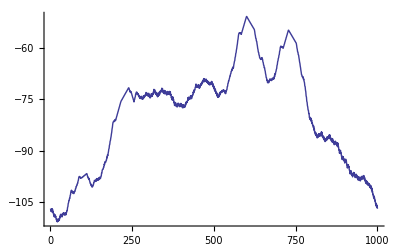

```mathematica
ListPlot[%,Joined->True]
```

```mathematica
S:={-438201/4099,-441209/4099,-439611/4099,-441791/4099,-438261/4099,-442243/4099,-438961/4099,-442945/4099,-441431/4099,-444937/4099,-444337/4099,-447873/4099,-445137/4099,-448145/4099,-445705/4099,-448413/4099,-447303/4099,-450795/4099,-450687/4099,-453521/4099,-451095/4099,-454091/4099,-450835/4099,-453491/4099,-451069/4099,-452557/4099,-450451/4099,-451991/4099,-448261/4099,-449289/4099,-445671/4099,-446717/4099,-444745/4099,-446735/4099,-446139/4099,-448173/4099,-445413/4099,-446421/4099,-443819/4099,-444523/4099,-443117/4099,-445093/4099,-443975/4099,-446013/4099,-443605/4099,-445565/4099,-443623/4099,-445597/4099,-442853/4099,-442841/4099,-440561/4099,-440589/4099,-436853/4099,-435865/4099,-432251/4099,-431287/4099,-428555/4099,-428547/4099,-425949/4099,-425979/4099,-422563/4099,-421555/4099,-418277/4099,-416971/4099,-416247/4099,-418227/4099,-417429/4099,-419433/4099,-417697/4099,-419663/4099,-418381/4099,-420345/4099,-418605/4099,-418587/4099,-417329/4099,-417329/4099,-414605/4099,-414595/4099,-411967/4099,-411979/4099,-410247/4099,-410213/4099,-408095/4099,-408123/4099,-405389/4099,-404381/4099,-401773/4099,-400461/4099,-399761/4099,-400787/4099,-400515/4099,-401545/4099,-400855/4099,-401863/4099,-401613/4099,-401642/4099,-400919/4099,-400930/4099,-400345/4099,-400370/4099,-399665/4099,-399660/4099,-399055/4099,-399072/4099,-398365/4099,-398360/4099,-397757/4099,-397786/4099,-397057/4099,-397052/4099,-396451/4099,-396462/4099,-397745/4099,-399752/4099,-399833/4099,-401840/4099,-401169/4099,-403138/4099,-402575/4099,-404608/4099,-405857/4099,-407832/4099,-407907/4099,-409904/4099,-409217/4099,-411176/4099,-410575/4099,-412570/4099,-411833/4099,-411804/4099,-409867/4099,-409850/4099,-407139/4099,-407094/4099,-404513/4099,-404496/4099,-404763/4099,-405764/4099,-404503/4099,-405512/4099,-402859/4099,-404802/4099,-402255/4099,-402936/4099,-403195/4099,-404160/4099,-402915/4099,-403916/4099,-401263/4099,-403240/4099,-400665/4099,-402634/4099,-401883/4099,-401830/4099,-399567/4099,-399356/4099,-395665/4099,-395608/4099,-392051/4099,-391696/4099,-390949/4099,-390924/4099,-388643/4099,-388622/4099,-384971/4099,-385898/4099,-382329/4099,-383310/4099,-382569/4099,-382538/4099,-380289/4099,-380266/4099,-376601/4099,-377544/4099,-373983/4099,-374936/4099,-372199/4099,-370170/4099,-367215/4099,-366198/4099,-362471/4099,-361418/4099,-357831/4099,-356800/4099,-354075/4099,-352056/4099,-349091/4099,-346756/4099,-343075/4099,-341052/4099,-337459/4099,-335156/4099,-334363/4099,-334298/4099,-333321/4099,-334238/4099,-332499/4099,-333426/4099,-331779/4099,-332720/4099,-330945/4099,-329866/4099,-328205/4099,-327170/4099,-325389/4099,-324304/4099,-322629/4099,-321570/4099,-319783/4099,-318734/4099,-317051/4099,-315998/4099,-314227/4099,-313140/4099,-311481/4099,-310438/4099,-309325/4099,-308946/4099,-307977/4099,-307628/4099,-306535/4099,-306166/4099,-305179/4099,-304826/4099,-303755/4099,-303372/4099,-302399/4099,-302060/4099,-300969/4099,-300592/4099,-299631/4099,-299280/4099,-298209/4099,-297864/4099,-296887/4099,-296544/4099,-295475/4099,-295098/4099,-294139/4099,-293824/4099,-294691/4099,-296276/4099,-297275/4099,-298880/4099,-297857/4099,-299460/4099,-298533/4099,-300148/4099,-301079/4099,-302724/4099,-303751/4099,-305422/4099,-306347/4099,-307984/4099,-309049/4099,-310712/4099,-308375/4099,-307758/4099,-305529/4099,-304560/4099,-301591/4099,-301948/4099,-299081/4099,-299450/4099,-299107/4099,-300796/4099,-300589/4099,-302060/4099,-301083/4099,-303660/4099,-302787/4099,-305164/4099,-304891/4099,-306552/4099,-304975/4099,-306182/4099,-304203/4099,-306846/4099,-304065/4099,-306728/4099,-305689/4099,-307688/4099,-305773/4099,-306952/4099,-303391/4099,-306054/4099,-303487/4099,-304896/4099,-302849/4099,-303848/4099,-301759/4099,-302114/4099,-299435/4099,-302424/4099,-299867/4099,-302496/4099,-301651/4099,-303618/4099,-301193/4099,-303046/4099,-300371/4099,-304300/4099,-302067/4099,-305640/4099,-303891/4099,-305874/4099,-303443/4099,-304502/4099,-300885/4099,-303892/4099,-301293/4099,-303962/4099,-300905/4099,-301856/4099,-298777/4099,-299404/4099,-295703/4099,-299692/4099,-296105/4099,-299740/4099,-298051/4099,-301012/4099,-299595/4099,-301992/4099,-299303/4099,-303272/4099,-301027/4099,-304662/4099,-301923/4099,-303930/4099,-301801/4099,-302860/4099,-299147/4099,-302160/4099,-298533/4099,-299946/4099,-297225/4099,-299202/4099,-296607/4099,-298060/4099,-294335/4099,-298350/4099,-294745/4099,-298712/4099,-297027/4099,-300002/4099,-298863/4099,-300756/4099,-297017/4099,-301008/4099,-297409/4099,-300090/4099,-298343/4099,-301338/4099,-299895/4099,-302540/4099,-298825/4099,-301840/4099,-298207/4099,-300902/4099,-299155/4099,-301146/4099,-299869/4099,-301892/4099,-298141/4099,-302138/4099,-298513/4099,-302464/4099,-301757/4099,-305740/4099,-304785/4099,-308166/4099,-304431/4099,-308422/4099,-304825/4099,-308472/4099,-307727/4099,-311722/4099,-311265/4099,-314932/4099,-311217/4099,-315204/4099,-311589/4099,-315264/4099,-313553/4099,-316208/4099,-314935/4099,-316794/4099,-313049/4099,-315738/4099,-312115/4099,-314638/4099,-313931/4099,-315616/4099,-315161/4099,-316504/4099,-312775/4099,-316090/4099,-312491/4099,-314156/4099,-313419/4099,-316098/4099,-315163/4099,-317682/4099,-313975/4099,-317592/4099,-313967/4099,-317440/4099,-315707/4099,-317048/4099,-315775/4099,-316786/4099,-313071/4099,-314600/4099,-310993/4099,-311934/4099,-310211/4099,-311538/4099,-309605/4099,-309332/4099,-305601/4099,-308616/4099,-305019/4099,-307518/4099,-305797/4099,-307130/4099,-304973/4099,-306980/4099,-303261/4099,-306886/4099,-303263/4099,-306728/4099,-303973/4099,-304308/4099,-302035/4099,-302506/4099,-298777/4099,-300216/4099,-296597/4099,-298888/4099,-296157/4099,-296484/4099,-293521/4099,-293210/4099,-289483/4099,-293432/4099,-289817/4099,-293394/4099,-291329/4099,-292998/4099,-291231/4099,-293192/4099,-290139/4099,-293766/4099,-290841/4099,-294472/4099,-291405/4099,-293078/4099,-290137/4099,-291090/4099,-288695/4099,-290356/4099,-287741/4099,-289100/4099,-286067/4099,-287698/4099,-284775/4099,-285912/4099,-282857/4099,-286230/4099,-283307/4099,-286620/4099,-284247/4099,-285938/4099,-283667/4099,-285334/4099,-283629/4099,-287274/4099,-285141/4099,-287512/4099,-285651/4099,-288650/4099,-286967/4099,-289496/4099,-287117/4099,-290104/4099,-287811/4099,-290466/4099,-288081/4099,-289748/4099,-287473/4099,-289286/4099,-286219/4099,-289906/4099,-286975/4099,-290592/4099,-288833/4099,-292814/4099,-291145/4099,-294412/4099,-292699/4099,-296688/4099,-294565/4099,-298226/4099,-296231/4099,-300226/4099,-298761/4099,-301190/4099,-299825/4099,-303818/4099,-301529/4099,-305200/4099,-302981/4099,-304948/4099,-303175/4099,-304414/4099,-300695/4099,-302736/4099,-299145/4099,-300918/4099,-298775/4099,-299600/4099,-298309/4099,-298776/4099,-297063/4099,-299058/4099,-297329/4099,-297836/4099,-296081/4099,-298118/4099,-296651/4099,-298592/4099,-297227/4099,-300202/4099,-297921/4099,-300904/4099,-298185/4099,-298170/4099,-296403/4099,-296106/4099,-292377/4099,-292210/4099,-288621/4099,-288298/4099,-285585/4099,-285598/4099,-283463/4099,-282220/4099,-279847/4099,-279840/4099,-277247/4099,-276936/4099,-274215/4099,-274252/4099,-271895/4099,-272748/4099,-270047/4099,-271038/4099,-268755/4099,-269750/4099,-266533/4099,-264530/4099,-262271/4099,-261282/4099,-257553/4099,-256542/4099,-252943/4099,-251932/4099,-248709/4099,-246716/4099,-243583/4099,-241292/4099,-237565/4099,-235552/4099,-231955/4099,-229640/4099,-228387/4099,-228400/4099,-227987/4099,-228966/4099,-228243/4099,-229222/4099,-228923/4099,-229942/4099,-228217/4099,-227180/4099,-225563/4099,-224582/4099,-222845/4099,-221844/4099,-220245/4099,-219224/4099,-217511/4099,-216508/4099,-214889/4099,-213914/4099,-212197/4099,-211170/4099,-209579/4099,-208618/4099,-208889/4099,-209914/4099,-210317/4099,-211326/4099,-211623/4099,-212616/4099,-213011/4099,-214046/4099,-214331/4099,-215310/4099,-215699/4099,-216710/4099,-216965/4099,-217958/4099,-218349/4099,-219334/4099,-219613/4099,-220612/4099,-220973/4099,-222000/4099,-222283/4099,-223228/4099,-223623/4099,-224646/4099,-226901/4099,-229898/4099,-231635/4099,-234620/4099,-234939/4099,-237936/4099,-238353/4099,-241370/4099,-243635/4099,-246598/4099,-248341/4099,-251334/4099,-251641/4099,-254644/4099,-255081/4099,-258076/4099,-258335/4099,-259320/4099,-259023/4099,-260050/4099,-258381/4099,-259328/4099,-257765/4099,-258774/4099,-260041/4099,-263024/4099,-263773/4099,-266752/4099,-267061/4099,-270036/4099,-269657/4099,-272666/4099,-273949/4099,-276896/4099,-278617/4099,-281618/4099,-281909/4099,-284896/4099,-284677/4099,-287632/4099,-286925/4099,-287896/4099,-286613/4099,-287612/4099,-284947/4099,-285900/4099,-283343/4099,-284344/4099,-283599/4099,-284572/4099,-284301/4099,-285258/4099,-283569/4099,-284532/4099,-282289/4099,-283294/4099,-282571/4099,-283518/4099,-282119/4099,-283118/4099,-279461/4099,-280438/4099,-276907/4099,-277878/4099,-275169/4099,-274150/4099,-271855/4099,-270866/4099,-267205/4099,-266156/4099,-262595/4099,-261596/4099,-258849/4099,-257834/4099,-255045/4099,-254024/4099,-250337/4099,-249310/4099,-245705/4099,-244696/4099,-243985/4099,-244910/4099,-244627/4099,-245624/4099,-244887/4099,-245876/4099,-245597/4099,-246566/4099,-244831/4099,-243812/4099,-242177/4099,-241176/4099,-239443/4099,-238380/4099,-236765/4099,-235766/4099,-234007/4099,-232998/4099,-231383/4099,-230360/4099,-228635/4099,-227610/4099,-225967/4099,-224986/4099,-225267/4099,-226232/4099,-226609/4099,-227616/4099,-227879/4099,-228872/4099,-229279/4099,-230260/4099,-230531/4099,-231530/4099,-231891/4099,-232924/4099,-233203/4099,-234160/4099,-234569/4099,-235590/4099,-235843/4099,-236844/4099,-237241/4099,-238228/4099,-238521/4099,-239526/4099,-239901/4099,-240926/4099,-243203/4099,-246176/4099,-247923/4099,-250942/4099,-251277/4099,-254268/4099,-254723/4099,-257714/4099,-259987/4099,-262972/4099,-264691/4099,-267722/4099,-270007/4099,-272968/4099,-275345/4099,-278362/4099,-278617/4099,-280632/4099,-280377/4099,-281858/4099,-280977/4099,-283968/4099,-283445/4099,-286456/4099,-287751/4099,-291712/4099,-292463/4099,-296482/4099,-298633/4099,-303626/4099,-304939/4099,-309912/4099,-311205/4099,-315178/4099,-316879/4099,-320388/4099,-320711/4099,-324678/4099,-324453/4099,-329448/4099,-328703/4099,-331676/4099,-330417/4099,-332884/4099,-330257/4099,-334250/4099,-332635/4099,-336578/4099,-335851/4099,-338796/4099,-338507/4099,-341170/4099,-339467/4099,-344438/4099,-342207/4099,-347126/4099,-346397/4099,-349390/4099,-347841/4099,-350686/4099,-348023/4099,-351986/4099,-349751/4099,-353776/4099,-351033/4099,-353022/4099,-350751/4099,-352232/4099,-348585/4099,-351606/4099,-348985/4099,-351702/4099,-348993/4099,-350944/4099,-347999/4099,-350002/4099,-346285/4099,-351260/4099,-347677/4099,-352590/4099,-350877/4099,-353852/4099,-352537/4099,-355374/4099,-352669/4099,-356638/4099,-354367/4099,-358142/4099,-355387/4099,-357370/4099,-355245/4099,-356704/4099,-352981/4099,-355988/4099,-352349/4099,-355068/4099,-352335/4099,-354302/4099,-351673/4099,-353688/4099,-349929/4099,-353932/4099,-350331/4099,-355258/4099,-353519/4099,-356498/4099,-355357/4099,-358214/4099,-354491/4099,-358464/4099,-354847/4099,-358892/4099,-357135/4099,-360122/4099,-358677/4099,-361872/4099,-358143/4099,-361184/4099,-357555/4099,-360244/4099,-358529/4099,-361498/4099,-360227/4099,-363250/4099,-359503/4099,-363508/4099,-359903/4099,-364864/4099,-364135/4099,-368132/4099,-367671/4099,-372028/4099,-368317/4099,-372304/4099,-368699/4099,-372402/4099,-371657/4099,-375662/4099,-375653/4099,-379456/4099,-375711/4099,-379726/4099,-376115/4099,-379774/4099,-378049/4099,-381350/4099,-380073/4099,-383768/4099,-380039/4099,-382720/4099,-379127/4099,-382160/4099,-381441/4099,-385764/4099,-385293/4099,-389648/4099,-385931/4099,-389264/4099,-385661/4099,-388680/4099,-387937/4099,-392256/4099,-392253/4099,-396580/4099,-392861/4099,-396510/4099,-392891/4099,-397066/4099,-395339/4099,-398450/4099,-397167/4099,-400280/4099,-396565/4099,-398570/4099,-394965/4099,-396972/4099,-395235/4099,-398894/4099,-397435/4099,-401122/4099,-397399/4099,-400718/4099,-397117/4099,-400086/4099,-398347/4099,-401876/4099,-400267/4099,-403804/4099,-400075/4099,-403720/4099,-400097/4099,-404256/4099,-401545/4099,-404684/4099,-402391/4099,-405068/4099,-401345/4099,-403338/4099,-399733/4099,-402730/4099,-400001/4099,-402840/4099,-399905/4099,-402412/4099,-398695/4099,-402656/4099,-399043/4099,-402652/4099,-401245/4099,-405162/4099,-404389/4099,-407570/4099,-404507/4099,-408158/4099,-405221/4099,-409028/4099,-406653/4099,-409664/4099,-407535/4099,-410386/4099,-407995/4099,-410640/4099,-408535/4099,-412196/4099,-409785/4099,-413208/4099,-411103/4099,-413784/4099,-411201/4099,-416154/4099,-413795/4099,-418726/4099,-417681/4099,-421686/4099,-421099/4099,-424626/4099,-422897/4099,-426570/4099,-425123/4099,-429134/4099,-428071/4099,-432090/4099,-431489/4099,-435246/4099,-432847/4099,-436830/4099,-434737/4099,-438388/4099}
pn[S]
i[%]
po[%]
Plot[%,{j,0,(Length[S]+1)}]
```

{{a_1→0,a_2→1}}

{0,1}

j

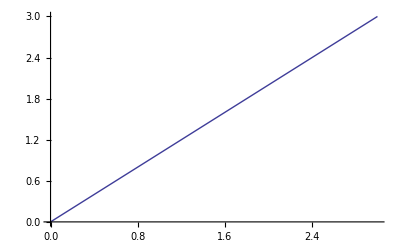

```mathematica
pn[s_]:=FindInstance[Table[Total[Table[Subscript[a, i]*j^(i-1),{i,1,Length[s]}]]==s[[j]],{j,1,Length[s]}],Table[Subscript[a, i],{i,1,Length[s]}],Reals]
i[in_]:=Table[Last[Flatten[in][[i]]],{i,1,Length[Flatten[in]]}]
po[s_]:=Total[Table[(s[[i]])*j^(i-1),{i,1,Length[s]}]]
S:={1,2}
pn[S]
i[%]
po[%]
Plot[%,{j,0,(Length[S]+1)}]
```